```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Image Histograms

```mathematica
allImagesColor[[13]]
```

Part::partd: Part specification allImagesColor⟦13⟧ is longer than depth of object.

allImagesColor⟦13⟧

At heart, digital images are made of collections of numbers. Humans much more easily perceive overall properties of an image: it’s too dark, the contrast is too low, the red/green balance is funny. One way to see the relationship between these disparate views is to use a histogram, which plots a graph of the values present in an image and how prevalent those values are. These graphs can be used to make automated decisions (from the data in the image) that mimic some of the kinds of decisions that humans might make. Alternatively, they can be useful to the observers in making decisions about what kinds of preprocessing might help in a given situation.

```mathematica
TableForm[{{Hyperlink["CanvasPatch",{"visualVocabHistograms.nb","CanvasPatch"}],labelCanvasPatch},{Hyperlink["CanvasPatchEQ",{"visualVocabHistograms.nb","CanvasPatchEQ"}],labelCanvasPatchEQ},{Hyperlink["Tally",{"visualVocabHistograms.nb","Tally"}],labelTally},{Hyperlink["ColorHistogram",{"visualVocabHistograms.nb","ColorHistogram"}],labelColorHistogram},{Hyperlink["ColorHistogramEQ",{"visualVocabHistograms.nb","ColorHistogramEQ"}],labelColorHistogramEQ},{Hyperlink["HistogramBinarization",{"visualVocabHistograms.nb","HistogramBinarization"}],labelHistogramBinarization},{Hyperlink["ColorHistogramBinarization",{"visualVocabHistograms.nb","ColorHistogramBinarization"}],labelColorHistogramBinarization},
{Hyperlink["Dither",{"visualVocabHistograms.nb","Dither"}],labelDither},{Hyperlink["BWHistEQ",{"visualVocabHistograms.nb","BWHistEQ"}],labelBWHistEQ},{Hyperlink["ColorHistEQ",{"visualVocabHistograms.nb","ColorHistEQ"}],labelColorHistEQ},{Hyperlink["HSBEqualEQ",{"visualVocabHistograms.nb","HSBEqualEQ"}],labelHSBEqualEQ}}]
```

| Plotting the rows of an image as a function
 | Stretching the values to utilize the full range from 0 (pure black) to 1 (pure white)
 | A histogram counts how many of each value occur
 | The histogram of an RGB image is three histograms: of the red values, of the green values, and of the blue values
 | The histogram of an HSB image is three histograms: of the hue values, of the saturation values, and of the brightness values
 | Histograms can be useful in helping to choose thresholds for binarization
 | Histograms can be useful in helping to choose thresholds for binarization of color images
 | Adding dither to the histogram-equalized image can help smooth out the jumps
 | A variety of x-ray images before and after histogram equalization
 | Histogram equalization of RGB color images can change the color dramatically
 | Applying histogram equalization to the brightness channel of an HSB image helps to maintain the integrity of the colors

Three important commands in this notebook are: ImageHistogram[ ] takes the histogram of an image and displays it, ImageAdjust[ ] allows simple command over the constrast and brightness (and other aspects) of an image, and Binarize[ ] turns a grayscale or color image into a black and white image, allowing some control over the process.

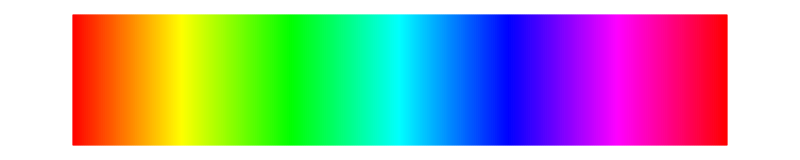

```mathematica
specLine
```

Here's an example that shows a small patch from a x-ray of F634. Move the small green box around to zoom into a 10 by 10 square of the image.

```mathematica
labelCanvasPatch="None of the white areas are completely white: the maximum value is about 0.8";infoCanvasPatch="A 10x10 patch of a larger x-ray is highlighted in green. Move the patch around using the mouse.\n\nCompare the patch at its real size (middle) and enlarged for easier viewing (right). The corresponding numerical representation (a 10x10 matrix) is shown at the bottom.\n\nObserve that none of the areas are truly white. What is the largest number you can find (i.e., the pixel closest to white)?\n\nLooking at the negative image, there are many pixels of pure white, but none that reach pure black.\n\nWhat is the smallest pixel value you can find in the negative image?";canvasPatch=ImageTake[Import[pathXray~~"F634Tile.tif"],100,100];gBox=Graphics[{Green,Thickness[0.2],Opacity[0.4],Polygon[{{1,1},{1,-1},{-1,-1},{-1,1}}]},ImageSize->20];Manipulate[If[invert=="negative",img=canvasPatch,img=ColorNegate[canvasPatch]];Row[{Image[img,ImageSize->200],Spacer[20],smallPatch=ImageTake[img,100-{Clip[pt[[2]]+5,{1,99}],Clip[pt[[2]]-4,{1,99}]},{Clip[pt[[1]]-4,{1,99}],Clip[pt[[1]]+5,{1,99}]}],Spacer[20],Image[smallPatch,ImageSize->{200,200}],Spacer[20],PaddedForm[MatrixForm[ImageData[smallPatch]],{2,2}]}],{{pt,{50,50}},Locator,LocatorAutoCreate->True,Appearance->gBox},Row[{Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoCanvasPatch]}],
FrameLabel->Style[labelCanvasPatch,Medium],TrackedSymbols->{pt,invert},SaveDefinitions->True]
```

The image on the left appears a bit dull: there are plenty of black areas that are truly black, but the white areas are not really completely white. Scanning through the image verifies this: the black areas correspond to numbers that are 0.00. The whitest areas are not much larger than 0.85. In fact, the largest value in the image is:

```mathematica
Max[Max[ImageData[canvasPatch]]]
```

0.823529

```mathematica
specLine
```

-Graphics-

It would surely make sense to stretch this out to utilize the full range of possible values from 0.00 (full black) to 1.00 (full white). This is easy to do:

```mathematica
labelCanvasPatchEQ="Stretching the values to utilize the full range from 0 (pure black) to 1 (pure white)";infoCanvasPatchEQ="A 100x100 section of an x-ray is equalized using the ImageAdjust[ ] function.\n\nObserve that the largest values are true white and the smallest values are true black.\n\nThe same is true in the negative image.";canvasPatchEQ=ImageAdjust[ImageTake[Import[pathXray~~"F634Tile.tif"],100,100]];gBox=Graphics[{Green,Thickness[0.2],Opacity[0.4],Polygon[{{1,1},{1,-1},{-1,-1},{-1,1}}]},ImageSize->20];Manipulate[If[invert=="negative",img=canvasPatchEQ,img=ColorNegate[canvasPatchEQ]];Row[{Image[img,ImageSize->200],Spacer[20],smallPatch=ImageTake[img,100-{Clip[pt[[2]]+5,{1,99}],Clip[pt[[2]]-4,{1,99}]},{Clip[pt[[1]]-4,{1,99}],Clip[pt[[1]]+5,{1,99}]}],Spacer[20],Image[smallPatch,ImageSize->{200,200}],Spacer[20],PaddedForm[MatrixForm[ImageData[smallPatch]],{2,2}]}],{{pt,{50,50}},Locator,LocatorAutoCreate->True,Appearance->gBox},Row[{Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoCanvasPatchEQ]}],
FrameLabel->Style[labelCanvasPatchEQ,Medium],TrackedSymbols->{pt,invert},SaveDefinitions->True]
```

HW: Build your own function to mimic the behavior of ImageAdjust[ ] by (a) find the largest and the smallest pixel values in the image (b) specify a point function that maps the smallest value to zero, the largest to one, and is a straight line in between (c) implement this in an interactive demonstration such as these point functions.

Comparing the two images in the above two demonstrations, it is clear that the second has better contrast. In addition, it would very likely also be easier to work with if one were to attempt to count the number of threads or otherwise study the image. This is an example of preprocessing: in this case, adjusting the contrast so as to make some task easier (whether visually or computationally). While in this case it was easy to see what needed to be done, this notebook discusses a method that helps to make such decisions easier to make. The histogram of an image shows concretely what kinds of adjustments to the image might make sense. When such computational insight is combined with visual insight, it is often possible to do better than either one alone.

```mathematica
specLine
```

-Graphics-

To see how this works, first consider the simple scenario where there are a large number of 1’s and 0’s. A natural thing to do is to tally up how many of each there are. The histogram is a plot of this tally: it will have two values, one showing how many 0’s occur and one showing how many ones occur. In the second scenario that data is a little more complicated, consisting of 100 numbers drawn from 0, 0.1,  0,2, 0.3, 0.4, 05, 0.6, 0.7, 0.8, 0.9, and 1. The tally counts up how many of each occur and then the histogram plots this.

```mathematica
labelTally="A histogram counts how many of each value occur";infoTally="Flip between binary and uniform, each time observing how many of each value occur in the tally.\n\nThe histogram is a plot of the tally.";
Manipulate[If[x=="binary",rand01=RandomChoice[{0,1},100];,rand01=RandomChoice[{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},100];];
count=Sort[Tally[rand01]];
Column[{"Random Numbers are:" ,rand01,"\nTally is:", count,"\nHistogram is:",Histogram[rand01,Length[count]]}],Row[{Control[{{x,"binary"},{"binary","uniform"}}],Spacer[20],info[infoTally]}],FrameLabel->Style[labelTally,Medium],SaveDefinitions->True]
```

In exactly the same way, the histogram can be applied to the canvas patch above. The large spike at the left indicates that there are a large number of pure black pixels (those with numerical value equal to 0). The hump at about the 2/3 point shows there are a large number of pixels with value around 0.7, and the drop off to the right shows that there are no pixel values above about 0.8.

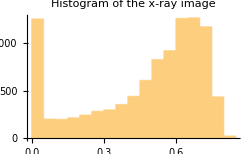

```mathematica
Histogram[Flatten[ImageData[canvasPatch]],ImageSize->250,PlotLabel->"Histogram of the x-ray image"]
```

After the image adjustment (sometimes called histogram equalization), the histogram has the same basic shape, but the values are spread out across the full range from 0 to 1 (notice the horizontal axis above goes from 0 to 0.8 while the horizontal axis below goes from 0 to 1).

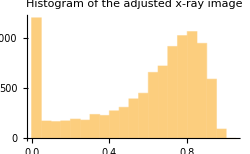

```mathematica
Histogram[Flatten[ImageData[canvasPatchEQ]],ImageSize->250,PlotLabel->"Histogram of the adjusted x-ray image"]
```

```mathematica
specLine
```

-Graphics-

When the image is in color, each of the pixel elements is a collection of three numbers representing the amount of red, green, and blue components. A histogram of a color image, then, is really three histograms, one of the red values, one of the green values, and one of the blue values.

```mathematica
labelColorHistogram="The histogram of an RGB image is three histograms: of the red values, of the green values, and of the blue values";infoColorHistogram="Look at the various pictures and observe how the three histograms give information about how much of each color is present in the image.\n\nIn Sunflowers there are lots of large red and green values and not very many large blue values. Explain.\n\nIn Milkmaid, there are very few pixel values near one (of any color). What does this tell about the picture?";
Manipulate[img=Image[allImagesColor[[i]]];
ImageHistogram[img];
GraphicsRow[{img,ImageHistogram[img,Appearance->"Separated"]},ImageSize->700],
Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}]Spacer[20],info[infoColorHistogram]}],
FrameLabel->Style[labelColorHistogram,Medium],TrackedSymbols->{i},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦9⟧ is longer than depth of object.

Image::imgarray: The specified argument allImagesColor⟦9⟧ should be an array of rank 2 or 3 with machine-sized numbers.

ImageHistogram::imginv: Expecting an image or graphics instead of Image[allImagesColor⟦9⟧].

Part::partd: Part specification allImagesColor⟦9⟧ is longer than depth of object.

Image::imgarray: The specified argument allImagesColor⟦9⟧ should be an array of rank 2 or 3 with machine-sized numbers.

ImageHistogram::imginv: Expecting an image or graphics instead of Image[allImagesColor⟦9⟧].

Part::partd: Part specification allImagesColor⟦9⟧ is longer than depth of object.

Image::imgarray: The specified argument allImagesColor⟦9⟧ should be an array of rank 2 or 3 with machine-sized numbers.

ImageHistogram::imginv: Expecting an image or graphics instead of Image[allImagesColor⟦9⟧].

HW: Alternatively, it is possible to form a histogram of an image based on the HSB representation. In this case, there are again three histograms, one of the hue values, one of the saturation values, and one of the brightness values. Generate a figure like the above where the three histograms are based on the HSB model.

Now that we have an idea of what histograms are, we can ask what good they are. The canvas patch above showed one possible application: the histogram can indicate a lack of contrast in the image.

```mathematica
specLine
```

-Graphics-

More generally, the histogram can help to pinpoint problems with an image: not enough dark pixels, too many red pixels, etc. In fact, there is a clear (visual) relationship between three common attributes of an image and the histograms. (1) Contrast: when all the values in the histogram clustered together in a small region, the contrast is too low. When many pixels are scattered at the ends of the histogram, the contrast is too high. In between too low and too high, when the values are spread out uniformly across the full range, the contrast tends to be best. (2) Brightness: fix the low end of the histogram values. Stretching or compressing the histograms directly effects how bright the image appears. (3) Both the brightness and the contrast correspond to stretching or compressing the range of the values occupied by the histogram. The "gamma" of the image changes the shape of the histogram, causing one section or another to bulge upwards. The effect is a deepening of the colors as gamma increases, and a washed out, desaturated effect as it is decreased. The following example allows manipulation of the contrast, brightness, and gamma of the image, and shows the corresponding effect on the red/green, and blue histograms.

```mathematica
labelColorHistogramEQ="The histogram of an HSB image is three histograms: of the hue values, of the saturation values, and of the brightness values";infoColorHistogramEQ="Each slider operates on the histogram of the image to accomplish a visual goal. Observe the effect of the control sliders on the images and on the histograms:\n\nThe contrast slider expands and contracts the histograms, oincreasing and decreasing the contrast.\n\nThe brightness slider squishes the histograms to the left, darkening the image.\n\nThe gamma slider leaves the ends of the histograms fixed and moves the center of mass of the histogram to the left and right, deepening the colors or making them paler.\n\nMoving the gamma slider far to the left or right causes large spikes at the right and left ends of the histograms. Explain what these spikes mean in terms of individual pixel values and in terms of the overall image.";
Manipulate[img=ImageAdjust[allImagesColor[[i]],{cont,bright,gam}];
GraphicsRow[{img,ImageHistogram[img,Appearance->"Separated"]},ImageSize->700],
Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoColorHistogramEQ]}],
{{cont,0,"contrast"},-1,2},{{bright,0,"brightness"},-1,1},{{gam,1,"gamma"},0.01,4},
FrameLabel->Style[labelColorHistogramEQ,Medium],TrackedSymbols->{i,cont,bright,gam},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦9⟧ is longer than depth of object.

ImageAdjust::imginv: Expecting an image or graphics instead of allImagesColor⟦9⟧.

ImageHistogram::imginv: Expecting an image or graphics instead of ImageAdjust[allImagesColor⟦9⟧,{0,0,1}].

Part::partd: Part specification allImagesColor⟦9⟧ is longer than depth of object.

ImageAdjust::imginv: Expecting an image or graphics instead of allImagesColor⟦9⟧.

ImageHistogram::imginv: Expecting an image or graphics instead of ImageAdjust[allImagesColor⟦9⟧,{0,0,1}].

```mathematica
specLine
```

-Graphics-

The next application of the histogram is to the binarization of images and to the choice of thresholds. The process of binarization means to turn a grayscale or a color image into a pure binary black and white image where all pixels have value equal to either zero or one. This is often done by choosing a threshold value: all numbers below the threshold are set to 0 (black) and all values above the threshold are set to 1 (white). If the threshold is set too low, the image becomes almost fully white. If set too high, the image becomes almost all black. In between too low and too high is often a value that works nicely. Sometimes this occurs near a peak in the histogram and sometimes it can occur near a valley in the histogram. In many cases the histogram can provide insight into how to best choose the threshold value.

```mathematica
labelHistogramBinarization="Histograms can be useful in helping to choose thresholds for separating high intensity features";infoHistogramBinarization="Try to choose threshold values that locate the peaks of the horizontal and vertical threads.\n\nCan you think of a rule (based on the shape of the histograms) that would help to choose this threshold?\n\nObserve that the histogram of the negative is flipped horizontally from the histogram of the positive.";
Manipulate[canvasPatch=ImageTake[allImagesXray[[i]],100,100];
If[invert=="negative",img=canvasPatch,img=ColorNegate[canvasPatch]];Row[{Image[img,ImageSize->250],Spacer[40],ImageHistogram[img,ImageSize->250,Epilog->{Red,Line[{{t,0},{t,10000}}]}],Spacer[40],Image[Binarize[img,t],ImageSize->250]}],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[10],Control[{{t,0.35,"threshold"},0,1}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoHistogramBinarization]}],
FrameLabel->Style[labelHistogramBinarization,Medium],TrackedSymbols->{i,t,invert},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesXray⟦7⟧ is longer than depth of object.

ImageTake::imginv: Expecting an image or graphics instead of allImagesXray⟦7⟧.

Image::imgarray: The specified argument ImageTake[allImagesXray⟦7⟧,100,100] should be an array of rank 2 or 3 with machine-sized numbers.

ImageHistogram::imginv: Expecting an image or graphics instead of ImageTake[allImagesXray⟦7⟧,100,100].

Binarize::imginv: Expecting an image or graphics instead of ImageTake[allImagesXray⟦7⟧,100,100].

Image::imgarray: The specified argument Binarize[ImageTake[allImagesXray⟦7⟧,100,100],0.35] should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification allImagesXray⟦7⟧ is longer than depth of object.

ImageTake::imginv: Expecting an image or graphics instead of allImagesXray⟦7⟧.

Image::imgarray: The specified argument ImageTake[allImagesXray⟦7⟧,100,100] should be an array of rank 2 or 3 with machine-sized numbers.

ImageHistogram::imginv: Expecting an image or graphics instead of ImageTake[allImagesXray⟦7⟧,100,100].

Binarize::imginv: Expecting an image or graphics instead of ImageTake[allImagesXray⟦7⟧,100,100].

Image::imgarray: The specified argument Binarize[ImageTake[allImagesXray⟦7⟧,100,100],0.35] should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification allImagesXray⟦7⟧ is longer than depth of object.

ImageTake::imginv: Expecting an image or graphics instead of allImagesXray⟦7⟧.

Image::imgarray: The specified argument ImageTake[allImagesXray⟦7⟧,100,100] should be an array of rank 2 or 3 with machine-sized numbers.

ImageHistogram::imginv: Expecting an image or graphics instead of ImageTake[allImagesXray⟦7⟧,100,100].

Binarize::imginv: Expecting an image or graphics instead of ImageTake[allImagesXray⟦7⟧,100,100].

Image::imgarray: The specified argument Binarize[ImageTake[allImagesXray⟦7⟧,100,100],0.35] should be an array of rank 2 or 3 with machine-sized numbers.

```mathematica
specLine
```

-Graphics-

When choosing thresholds to binarize color images, it can also be helpful to look at the histograms.

```mathematica
labelColorHistogramBinarization="Histograms can be useful in helping to choose thresholds for binarization of color images";infoColorHistogramBinarization="In the sunflowers, observe how the threshold can sensibly be chosen to remove most of the blue pixels and keep most of the red pixels.\n\nSimilarly, a good choice for the Sheep Shearer is the point where the blue and the red histograms cross.";
Manipulate[
GraphicsRow[{allImagesColor[[i]],ImageHistogram[allImagesColor[[i]],Appearance->"Transparent",Epilog->{Red,Line[{{t,0},{t,10000}}]}],Image[Binarize[allImagesColor[[i]],t]]},ImageSize->800],Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[10],Control[{{t,0.5,"threshold"},0,1}],Spacer[20],info[infoColorHistogramBinarization]}],FrameLabel->Style[labelColorHistogramBinarization,Medium],
TrackedSymbols->{i,t},SaveDefinitions->saveDef]
```

HW: When dealing with color images, it may also make sense to have three separate thresholds, one for the red, one for the green and one for the blue channels. A direct implementation of this would result in three separate binary images, one of each channel. Implement this method and explain how the three thresholds could be combined to achieve a single binary image.

HW: When dealing with color images, it may also make sense to have three separate thresholds, one for the hue, one for the saturation and one for the brightness channels. A direct implement of this would result in three separate binary images, one of each channel. Implement this method and explain how the three thresholds could be combined to achieve a single binary image.

```mathematica
specLine
```

-Graphics-

The final application of the histogram is a more sophisticated kind of contrast enhancement called histogram equalization. The idea is that in many applications, “good” images have a histogram that is roughly even across the range of values from 0 to 1. Histogram equalization change the values of the image so as to spread the histogram out to use the full range of possible values. For example, the low-contrast eye picture

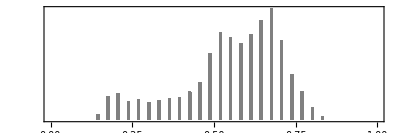

```mathematica
GraphicsRow[{eye=-Graphics-,ImageHistogram[eye]},ImageSize->500,PlotLabel->"The histogram of Lena's eye reaches neither to zero (pure blacks) nor 1 (pure white)"]
```

becomes the higher contrast image:

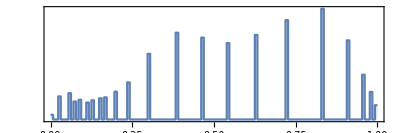

```mathematica
eyeMat=ImageData[eye][[All,All,1]]; GraphicsRow[{Image[histEQ[eyeMat],"Byte"],ImageHistogram[Image[histEQ[eyeMat],"Byte"]]},ImageSize->500,PlotLabel->"The process of histogram equalization spreads the values out over the whole range"]
```

There is something odd about the resulting histogram: it has many large gaps, which represent possible pixel values that never occur in the image. This may or may not be a problem. If it is (for example, if only a small number of possible values occur, then the image may appear striated) it is possible to add a small amount of noise (called dither) that will perturb the values in the image slightly so as to fill in the empty spaces in the histogram. In this graphic, the parameter σ represents the amount of dither added. When σ is near zero, the image is the same as with standard histogram equalization. When σ is large, the image becomes noisy. With small amounts of dither, the smoothing of the histogram may improve the appearance of the image; with larger amounts of dither, the jittering of the pixels may appear as speckled noise.

```mathematica
labelDither="Adding dither to the histogram-equalized image can help smooth out the jumps";infoDither="Increase the dither until the picture looks as natural as possible.\n\nThis point correponds (more or less) with the value at which the holes are just filled.";
Manipulate[eyeDither=Clip[eyeMat+RandomVariate[NormalDistribution[0,σ^2],Dimensions[eyeMat]],{0,1}];
GraphicsRow[{Image[histEQ[eyeDither],"Byte"],ImageHistogram[Image[histEQ[eyeDither],"Byte"]]},ImageSize->500],Row[{Control[{{σ,0.001,"dither"},0.0001,0.15}],Spacer[20],info[infoDither]}],FrameLabel->Style[labelDither,Medium],TrackedSymbols->{σ},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Here are a variety of x-ray images and their equalized versions:

```mathematica
labelBWHistEQ="A variety of x-ray images before and after histogram equalization";infoBWHistEQ="Histogram equalization is like contrast on steroids -- and it can be done automatically without a human judgement of a parameter value.\n\nNotice that each tile becomes has better constrast as the histogram is spread out across the full range of possible values.";
Manipulate[
If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
histEQRGB=Image[histEQ[ImageData[img]],"Byte"];
GraphicsRow[{img,ImageHistogram[img,Appearance->"Separated"],ImageHistogram[histEQRGB,Appearance->"Separated"],histEQRGB},ImageSize->900],Row[{Control[{{i,3,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoBWHistEQ]}],
FrameLabel->Style[labelBWHistEQ,Medium],TrackedSymbols->{i,invert},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesXray⟦3⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allImagesXray⟦3⟧.

Image::imgarray: The specified argument histEQ[ImageData[allImagesXray⟦3⟧]] should be an array of rank 2 or 3 with machine-sized numbers.

ImageHistogram::imginv: Expecting an image or graphics instead of allImagesXray⟦3⟧.

ImageHistogram::imginv: Expecting an image or graphics instead of Image[histEQ[ImageData[allImagesXray⟦3⟧]],Byte].

Part::partd: Part specification allImagesXray⟦3⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allImagesXray⟦3⟧.

Image::imgarray: The specified argument histEQ[ImageData[allImagesXray⟦3⟧]] should be an array of rank 2 or 3 with machine-sized numbers.

ImageHistogram::imginv: Expecting an image or graphics instead of allImagesXray⟦3⟧.

ImageHistogram::imginv: Expecting an image or graphics instead of Image[histEQ[ImageData[allImagesXray⟦3⟧]],Byte].

```mathematica
specLine
```

-Graphics-

Equalizing color images is a bit more tricky. Applying the same histogram equalization routine to the red, green and blue channels separately can be quite effective if all three colors have similar histograms (in which case the equalization operates similarly on all three channels). However, when the histograms of the three colors are quite different, equalization can change the colors in the image drastically. While this may sometimes be an interesting special effect, it is rarely desirable.

```mathematica
labelColorHistEQ="Histogram equalization of RGB color images can change the color dramatically";infoColorHistEQ="Colors may change dramatically when the RGB channels are equalized separately.\n\nExample: the floor of the bedroom becomes almost purple.\nExample: all the yellow is drained from the sunflowers.";
Manipulate[img=allImagesColor[[i]];
{imgR,imgG,imgB}=ColorSeparate[img];histEQRGB=ColorCombine[{Image[histEQ[ImageData[imgR]],"Byte"],Image[histEQ[ImageData[imgG]],"Byte"],Image[histEQ[ImageData[imgB]],"Byte"]}];
GraphicsRow[{img,ImageHistogram[img,Appearance->"Separated"],ImageHistogram[histEQRGB,Appearance->"Separated"],histEQRGB},ImageSize->900],Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoColorHistEQ]}],SynchronousUpdating->False,
FrameLabel->Style[labelColorHistEQ,Medium],TrackedSymbols->{i},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦9⟧ is longer than depth of object.

ColorSeparate::imginv: Expecting an image or graphics instead of allImagesColor⟦9⟧.

Set::shape: Lists {imgR,imgG,imgB} and ColorSeparate[allImagesColor⟦9⟧] are not the same shape.

ImageData::imginv: Expecting an image or graphics instead of imgR.

Image::imgarray: The specified argument histEQ[ImageData[imgR]] should be an array of rank 2 or 3 with machine-sized numbers.

ImageData::imginv: Expecting an image or graphics instead of imgG.

Image::imgarray: The specified argument histEQ[ImageData[imgG]] should be an array of rank 2 or 3 with machine-sized numbers.

ImageData::imginv: Expecting an image or graphics instead of imgB.

General::stop: Further output of ImageData::imginv will be suppressed during this calculation.

Image::imgarray: The specified argument histEQ[ImageData[imgB]] should be an array of rank 2 or 3 with machine-sized numbers.

General::stop: Further output of Image::imgarray will be suppressed during this calculation.

ColorCombine::ccbinput: {Image[histEQ[ImageData[imgR]],Byte],Image[histEQ[ImageData[imgG]],Byte],Image[histEQ[ImageData[imgB]],Byte]} should be a list of images with the same image dimensions.

ImageHistogram::imginv: Expecting an image or graphics instead of allImagesColor⟦9⟧.

ImageHistogram::imginv: Expecting an image or graphics instead of ColorCombine[{Image[histEQ[ImageData[imgR]],Byte],Image[histEQ[ImageData[imgG]],Byte],Image[histEQ[ImageData[imgB]],Byte]}].

```mathematica
specLine
```

-Graphics-

One way to improve this is to apply the histogram equalization to the Brightness channel in the HSB representation, leaving the hue and saturation unchanged. This will tend to have the desired effect of increasing the contrast without effecting the color balance. Many of Van Gogh’s paintings already have a brightness channel that is fairly close to uniform so the equalization does not have much effect. But some, like the sunflower and the bedroom do change significantly. In these cases, it is easy to see that the hue and saturation of the image remains the same, while the brightness expands to be more nearly uniform.

```mathematica
labelHSBEqualEQ="Applying histogram equalization to the brightness channel of an HSB image helps to maintain the integrity of the colors";infoHSBEqualEQ="Applying equalization only to the brightness channel of the HSB representation can help to preserve the colors.\n\nExample: the contrast is increased in the sunflowers but they remain yellow.\n\nExample: the floor of the bedroom is a high contrast brown.\n\nIn the love letter, the original is dark around the edges; equalization brings out the detail in the (formerly dark) regions and preserves the clarity in the center. With such a large contrast changes, there are changes in color, even though the hue remains unchanged.";
Manipulate[img=allImagesColor[[i]];
imgHSB=ColorConvert[img,"HSB"];
{imgH,imgS,imgB}=ColorSeparate[imgHSB];
histEQHSB=Image[ColorCombine[{imgH, imgS,Image[histEQ[ImageData[imgB]],"Byte"]}],ColorSpace->"HSB"];
GraphicsRow[{imgHSB,ImageHistogram[imgHSB,Appearance->"Separated"],ImageHistogram[histEQHSB,Appearance->"Separated"],histEQHSB},ImageSize->900],Row[{Control[{{i,vermeerLove,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoHSBEqualEQ]}],SynchronousUpdating->False,
FrameLabel->Style[labelHSBEqualEQ,Medium],SynchronousUpdating->False,TrackedSymbols->{i},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦13⟧ is longer than depth of object.

ColorConvert::ccvinput: allImagesColor⟦13⟧ should be a valid image, a color directive, a list of machine-sized real numbers of length up to 5, or a list of such objects.

ColorSeparate::imginv: Expecting an image or graphics instead of ColorConvert[allImagesColor⟦13⟧,HSB].

Set::shape: Lists {imgH,imgS,imgB} and ColorSeparate[ColorConvert[allImagesColor⟦13⟧,HSB]] are not the same shape.

ImageData::imginv: Expecting an image or graphics instead of imgB.

Image::imgarray: The specified argument histEQ[ImageData[imgB]] should be an array of rank 2 or 3 with machine-sized numbers.

ColorCombine::ccbinput: {imgH,imgS,Image[histEQ[ImageData[imgB]],Byte]} should be a list of images with the same image dimensions.

Image::imgarray: The specified argument ColorCombine[{imgH,imgS,Image[histEQ[ImageData[imgB]],Byte]}] should be an array of rank 2 or 3 with machine-sized numbers.

ImageHistogram::imginv: Expecting an image or graphics instead of ColorConvert[allImagesColor⟦13⟧,HSB].

ImageHistogram::imginv: Expecting an image or graphics instead of Image[ColorCombine[{imgH,imgS,Image[histEQ[ImageData[imgB]],Byte]}],ColorSpace→HSB].

HW: In an image like L30, there are not many different values in the brightness channel. Accordingly, when doing histogram equalization, there are a large number of “empty” spaces in the equalized version, as you can see from the bottom histogram plot above. Your goal in this project is to create a modified histogram equalization method that “fills in” these empty spaces in the histogram. You may wish to begin with the following code, which shows the myHistEQ[ ] function, ready for your modifications.

```mathematica
myHistEQ[iMat_]:=Module[{},
pixels=Round[255 Flatten[iMat]];
{h,w}=Dimensions[iMat];
hPDF=BinCounts[pixels,{0,256,1}]/(h*w);
hCDF=Accumulate[hPDF];
outPix=hCDF[[pixels+1]];
Partition[outPix,w]];
```